```mathematica
RatioPenalty[x_,y_,u_,v_]:=1+u/x+v/y(*(x/y-u/v)+(y/x-v/u)*)
```

```mathematica
Plot3D[{
RatioPenalty[x,y,1,1],
RatioPenalty[x,y,0.1,0.5]
},{x,0,1},{y,0,1},
PlotRange->{0,10},
ClippingStyle->None,
PlotPoints->50,
PlotStyle->{Yellow,Blue}]
```

-Graphics3D-

```mathematica
f[x_]:= Norm[x]
D[f[x]^2,x]
```

2 Norm[x] Norm'[x]

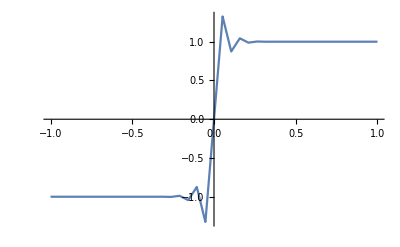

```mathematica
Plot[ Norm'[x],{x,-1,1}]
```

```mathematica
before = {0.5,0.5};
after[{x_,y_},{u_,v_}]:=(1+v/y+u/x)*Norm[{x,y}-{u,v}]^2
Plot3D[{after[{x,y},before]},{x,0,1},{y,0,1},
PlotRange->{0,1},
PlotPoints->100,
MeshFunctions->{#3&},
ClippingStyle->None]
```

-Graphics3D-

```mathematica
perpTo[{x_,y_},{a_,b_,c_}, val0_]:= -(a*x+b*y)/c+val0
```

```mathematica
Plot3D[{
perpTo[{x,y},{0,-2,5},0.1],
perpTo[{x,y},{-2,0,5},0.1]
},{x,0,1},{y,0,1},
PlotRange->{0,1},
PlotPoints->100,
MeshFunctions->{#3&},
ClippingStyle->None]
```

-Graphics3D-